```mathematica
(* 
Terahertz wave propagation in uniform nanorods:A nonlocal continuum
mechanics formulation including the effect of lateral inertia
S.Narendar
 *)
```

```mathematica
Needs["PlotLegends`"]
Clear[Evaluate[Context[]<>"*"]];
SetOptions[Plot,
PlotStyle->{{Thick},{Thick, Dashed},{Thick, Dotted},{Thick, DotDashed},{Thick, Dashing[0.05]},{Thick, Dashing[0.1]}},
LabelStyle->{FontFamily->"Arial",
FontSize->10},
Frame->True
];
SetOptions["PlotLegend",{"Classical/Local Rod Model","Nonlocal second order strain gradient model",
"Nonlocal fourth order strain gradient model",
"Nonlocal stress gradient model","Born-Karman model",
"NL Stress Gr with Inertia"
}];
SetOptions["LegendShadow", None];
SetOptions["ImageSize",Large];
SetOptions["LegendPosition",{-0.5,-1.65}]
```

```mathematica
u[x_,t_]:= Exp[-I(k x - ω t)]
ωCl[k_]=Solve[D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωStrainG[k_]=Solve[α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStrain4G[k_]=Solve[ α^4 D[u[x,t],{x,6}]+ α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStressG[k_]= Solve[D[u[x,t],{x,2}]+(ρ/Ev)α^2 D[D[u[x,t],{t,2}],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωBK[k_]=(2/0.142)Sqrt[Ev/ρ]Sin[k * 0.142/2];
ωStressGIn[k_]=Solve[Ev D[u[x,t],{x,2}]== ρ D[u[x,t],{t,2}] - ρ ν^2ζ^2 D[D[u[x,t],{t,2}],{x,2}]-α^2 ρ D[D[u[x,t],{t,2}],{x,2}]+α^2 ρ ν^2ζ^2D[D[u[x,t],{t,2}],{x,4}],ω][[2,1,2]]
```

(√Ev k)/(√(1+k^2 α^2+k^2 ζ^2 ν^2+k^4 α^2 ζ^2 ν^2) √ρ)

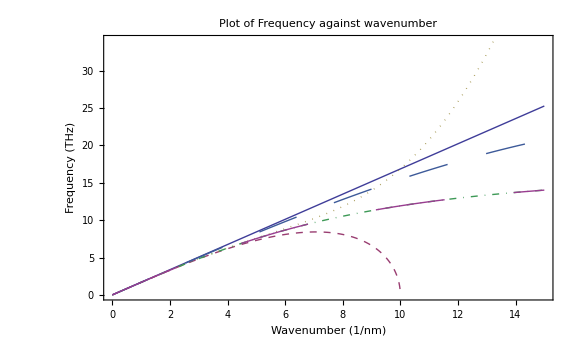

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
α= 0.1 ,
r = 3.5 * 10^(-9),
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280,
ζ = 0.238095 10^(-9)
},


Plot[{ωCl[k]/(1000 4 Pi),ωStrainG[k]/(1000 4 Pi),ωStrain4G[k]/(1000 4 Pi),ωStressG[k]/(1000 4 Pi),ωBK[k]/(1000 4 Pi),ωStressGIn[k]/(1000 4 Pi)},{k,0,15},
PlotLabel->"Plot of Frequency against wavenumber",
Frame->True,
FrameLabel->{"Wavenumber (1/nm)","Frequency (THz)"},
PlotLegend->{"Local Model","NL  II order strain gradient",
"NL 4th order strain gradient",
"NL stress gradient model","Born-Karman model","NL Stress Gr with Inertia"
},
LegendShadow->None,
LegendPosition->{-0.5,-1.65},
LegendSize->{1.5,1},
ImageSize->Large
]
]
```

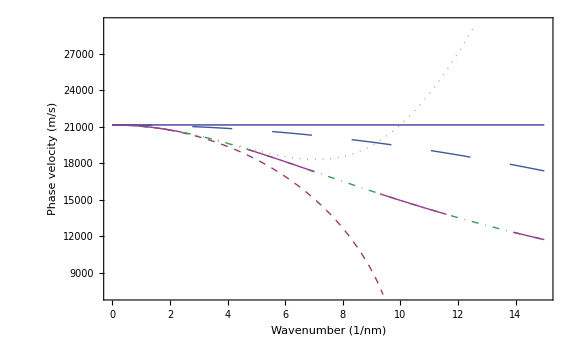

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
α= 0.1 ,
r = 3.5 * 10^(-9),
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280,
ζ = 0.238095 10^(-9)
},

(* Group Velocity *)
VgCl[x_]=ωCl[x]/x;
VgStrainG[x_]=ωStrainG[x]/x;
VgStrain4G[x_]=ωStrain4G[x]/x;
VgStressG[x_]=ωStressG[x]/x;
VgBK[x_]=ωBK[x]/x;
VgStressGIn[x_]=ωStressGIn[x]/x;

Plot[{VgCl[k],VgStrainG[k],VgStrain4G[k],VgStressG[k],VgBK[k],VgStressGIn[k]},{k,0,15},
FrameLabel->{"Wavenumber (1/nm)","Phase velocity (m/s)"},
PlotLegend->{"Local Model","NL  II order strain gradient",
"NL 4th order strain gradient",
"NL stress gradient model","Born-Karman model","NL Stress Gr with Inertia"
},
LegendShadow->None,
LegendPosition->{-0.5,-1.65},
LegendSize->{1.5,1},
ImageSize->Large
]
]
```

```mathematica
Group Velocity Calculation and Plot
```

and Calculation Group Plot Velocity

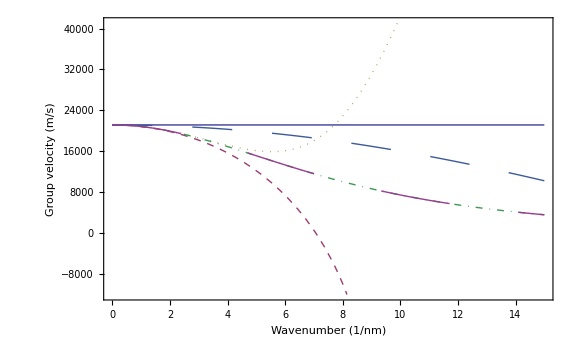

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
α= 0.1 ,
r = 3.5 * 10^(-9),
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280,
ζ = 0.238095 10^(-9)
},

VgCl[x_]=D[ωCl[x],x];
VgStrainG[x_]=D[ωStrainG[x],x];
VgStrain4G[x_]=D[ωStrain4G[x],x];
VgStressG[x_]=D[ωStressG[x],x];
VgBK[x_]=D[ωBK[x],x];
VgStressGIn[x_]=D[ωStressGIn[x],x];

Plot[{VgCl[k],VgStrainG[k],VgStrain4G[k],VgStressG[k],VgBK[k],VgStressGIn[k]},{k,0,15},
FrameLabel->{"Wavenumber (1/nm)","Group velocity (m/s)"},
PlotLegend->{"Local Model","NL  II order strain gradient",
"NL 4th order strain gradient",
"NL stress gradient model","Born-Karman model","NL Stress Gr with Inertia"
},
LegendShadow->None,
LegendPosition->{-0.5,-1.65},
LegendSize->{1.5,1},
ImageSize->Large
]
]
```

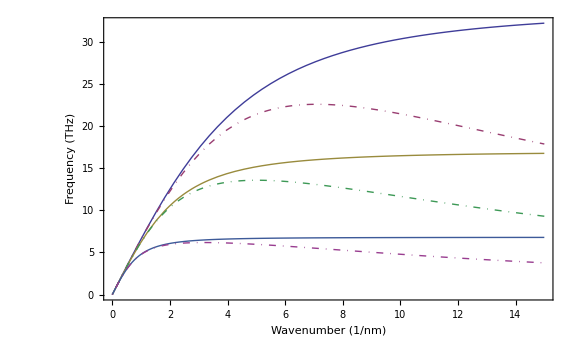

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
(*α= 0.1 ,*)
(*r = 3.5 * 10^(-9),*)
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280, (* Poisson's ratio *)
L=0.238 10^(-9)
},
ζ = Sqrt[(r^2)/2+(L^2)/12]; (* Radius of gyration of a cylindrical rod *)
Plot[
{(ωStressGIn[x]/(1000 Pi)/.{α->0,r->1}),(ωStressGIn[x]/.{α->0.1,r->1})/(1000 Pi),(ωStressGIn[x]/.{α->0,r->2})/(1000 Pi),(ωStressGIn[x]/.{α->0.1,r->2})/(1000 Pi),(ωStressGIn[x]/.{α->0,r->5})/(1000 Pi),(ωStressGIn[x]/.{α->0.1,r->5})/(1000 Pi)},
{x,0,15},
PlotRange->Full,
PlotStyle->{{Thick},{Thick,DotDashed},{Thick},{Thick,DotDashed},
{Thick},{Thick,DotDashed}},
FrameLabel->{"Wavenumber (1/nm)","Frequency (THz)"},
ImageSize->Large
]
]
```

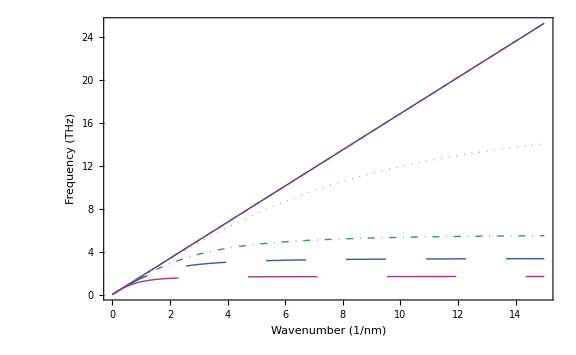

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
(*α= 0.1 ,*)
r = 3.5 * 10^(-9),
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280, (* Poisson's ratio *)
L=0.238 10^(-9)
},
ζ = Sqrt[(r^2)/2+(L^2)/12]; (* Radius of gyration of a cylindrical rod *)
Plot[
{(ωCl[x]/(4000 Pi)),(ωStressGIn[x]/(4000 Pi)/.α->0),
(ωStressGIn[x]/.α->0.1)/(4000 Pi),(ωStressGIn[x]/.α->0.3)/(4000 Pi),(ωStressGIn[x]/.α->0.5)/(4000 Pi),(ωStressGIn[x]/.α->1)/(4000 Pi)},
{x,0,15},
PlotRange->Full,
FrameLabel->{"Wavenumber (1/nm)","Frequency (THz)"},
PlotLegend->{"Local Model","e0a = 0 nm",
"e0a = 0.1 nm",
"e0a = 0.3 nm","e0a = 0.5 nm","e0a = 1.0 nm"
},
LegendShadow->None,
LegendPosition->{-0.5,-1.65},
LegendSize->{1.5,1},
ImageSize->Large
]
]
```